```mathematica
FisherSpeed[m_,s_,K_]:=1/2*Sqrt[s*m*K/2]
HVSpeed[m_,s_,K_]:=1/2*Sqrt[s*(s+1)*m*K/2]
```

```mathematica
Sweep[c0_,c1_]:=(c1-c0)/c1
```

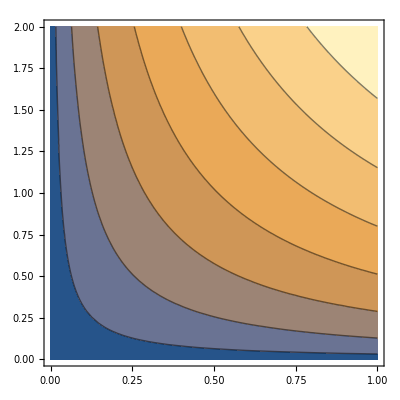

```mathematica
ContourPlot[FisherSpeed[m,s,10],{m,0,1},{s,0,2}]
```

```mathematica
K=100
m=0.1
s=0.1
```

100

0.1

0.1

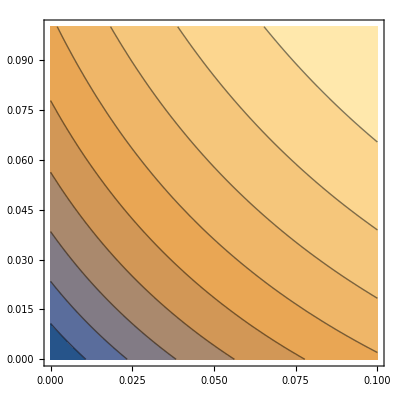

```mathematica
ContourPlot[Sweep[FisherSpeed[m,s,K],FisherSpeed[m+dm,s+ds,K]],{dm,0,0.1},{ds,0,0.1}]
```